```mathematica
(*This code generates the numbers for the 7th calculation in Section V of the revision of "Bounded extremum seeking for static quadratic maps using nonlinear transformation and Lyapunov method".*)

k1=-0.01;
k2=-0.01;
a11=.2;
a21=.2;
e1=0.36;
L1=2;
```

```mathematica
newrror2=NDSolve[{x1'[t]==(2k1/a11)*Sin[(2Pi/e1)*t]*((x1[t]+a11*Sin[(2Pi/e1)t])^2+(x2[t]+a21*Sin[(2*L1*Pi/e1)t])^2),
x2'[t]==(2k2/a21)*Sin[(L1*2Pi/e1)*t]*((x1[t]+a11*Sin[(2Pi/e1)t])^2+(x2[t]+a21*Sin[(2*L1*Pi/e1)t])^2),
x1[t/;t≤0]==1,x2[t/;t≤0]==-1},{x1,x2},{t,0,3200},MaxSteps->1000000,  AccuracyGoal->3,PrecisionGoal->8];
```

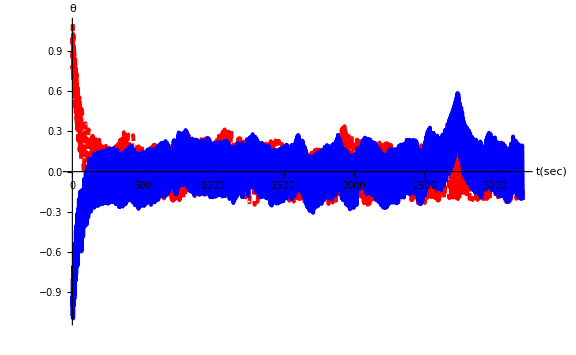

```mathematica
P1=Plot[x1[t]+a11*Sin[(2Pi/e1)t]/.newrror2,{t,0,3200},    AxesLabel->{ t [sec], θ },  AxesStyle->Thick,PlotStyle->{Dashed, Thickness[0.0049],RGBColor[1,0,0]},PlotRange->{{0,3200},{-1.1,1.1}}, LabelStyle->{FontFamily->"Times",FontSize ->20,FontWeight->"Bold",FontColor->Black},ImageSize->Large];

P2=Plot[x2[t]+a21*Sin[(2*L1*Pi/e1)t]/.newrror2,{t,0, 3200},   AxesLabel->{ t [sec], θ  },  AxesStyle->Thick,PlotStyle->{ Thickness[0.0049],RGBColor[0,0,1]},PlotRange->{{0,3200},{-1.1,1.1}}, LabelStyle->{FontFamily->"Times",FontSize ->20,FontWeight->"Bold",FontColor->Black},ImageSize->Large];

Show[P1,P2]
```